# Reaction function proposal (Dynamic centers generation)

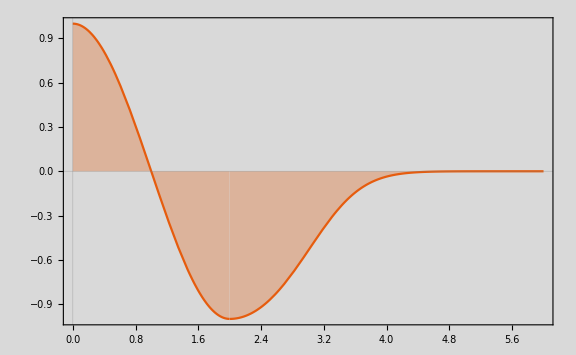

```mathematica
f1[x_]=Cos[π/2 x];
f2[x_]=-2/(1+ⅇ^((-2+x)^2));
f[x_]=Piecewise[{{f1[x],0<=x<2},{f2[x],2<=x}}];
Plot[f[x],{x,0,6},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```